# Lecture 12 - Conductors

### A Puzzle...

#### Divergence of the Curl

Prove that for any vector field A⃗ with continuous derivatives, OverVector[∇]·(OverVector[∇]×A⃗)=OverVector[0]. 
Hint: Consider the surface S shown below bounded by the curve C. Consider the line integral around C and invoke Stoke's Theorem and Gauss's Theorem with suitable arguments. Recall that these two theorems are

∫_curve A⃗·ⅆ s⃗=∫_surface (OverVector[∇]×A⃗)·ⅆ a⃗
∫_surface F⃗·ⅆ a⃗=∫_volume OverVector[∇]·F⃗ⅆv

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Of course, we could compute the divergence of a curl directly. For example, in Cartesian coordinates, A⃗=⟨A_x,A_y,A_z⟩ and we find

OverVector[∇]·(OverVector[∇]×A⃗)=⟨∂/(∂x),∂/(∂y),∂/(∂z)⟩·⟨(∂A_z)/(∂y)-(∂A_y)/(∂z),(∂A_x)/(∂z)-(∂A_z)/(∂x),(∂A_y)/(∂x)-(∂A_x)/(∂y)⟩
=∂/(∂x)(∂A_z)/(∂y)-∂/(∂x)(∂A_y)/(∂z)+∂/(∂y)(∂A_x)/(∂z)-∂/(∂y)(∂A_z)/(∂x)+∂/(∂z)(∂A_y)/(∂x)-∂/(∂z)(∂A_x)/(∂y)
=(∂/(∂y)(∂A_x)/(∂z)-∂/(∂z)(∂A_x)/(∂y))+(∂/(∂z)(∂A_y)/(∂x)-∂/(∂x)(∂A_y)/(∂z))+(∂/(∂x)(∂A_z)/(∂y)-∂/(∂y)(∂A_z)/(∂x))
=0

where the last step follows from the fact that the partial derivative operation commutes (i.e. taking ∂/(∂x)∂/(∂y) is the same as taking ∂/(∂y)∂/(∂x)) for any function with continuous derivatives.

However, we can be much more inspired and actually follow the hint in the problem. The idea is very simply to make C infinitesimally thin so that the curve C becomes a line that goes forward and then back along itself. In this limit, the surface S becomes a closed surface, and so we find

∫_C A⃗·ⅆ s⃗=∫_S (OverVector[∇]×A⃗)·ⅆ a⃗=∫_V OverVector[∇]·(OverVector[∇]×A⃗)ⅆv

where V is the volume enclosed by S. Because C goes back along itself, the line integral ∫_C A⃗·ⅆ s⃗=0=∫_V OverVector[∇]·(OverVector[∇]×A⃗)ⅆv. This analysis can be repeated on any infinitesimal volume in space, which proves that

OverVector[∇]·(OverVector[∇]×A⃗)=0

everywhere in space (for if OverVector[∇]·(OverVector[∇]×A⃗)≠0 at some point, we could pick a volume small enough around that point so that OverVector[∇]·(OverVector[∇]×A⃗) is essentially constant, so that there would be no possibility of any cancellation happening, and then we would reach a contradiction).

This result essentially boils down to the fact that the boundary of a boundary is zero. In other words, the boundary S of V has a boundary C which doesn’t exist (you can either make C a line that goes back on itself as we did above, or simply make it a line of zero length). □

### A 30,000 Foot View

It is important to realize that although we have been focusing specific charge distributions from points, lines, sheets, and spheres, electricity is one of the most prevalent and influential forces that we encounter in our daily lives. Often times, we do not appreciate the fact that nearly every action we take - from using our five senses to the interactions between bubbles to the mechanism underlying printers to the fact that we do not fall through the ground - is connected to electricity. For example, this remarkable YouTube video highlights some amazing electricity phenomena that you can easily test out for yourself!

So where are we in our study of electricity? Over the past few weeks, we have built up a lot of intuition about electrostatics, determining the electric field (E⃗) and electric potential (ϕ) from many different charge distributions (ρ). The relations between these three key quantities is summarized in the following diagram:

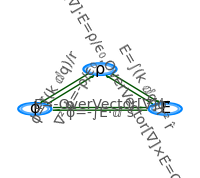

```mathematica
colors={RGBColor[0, 0.52, 1],RGBColor[Rational[1, 3], 0.6799999999999999, 1],GrayLevel[0.32],RGBColor[0, 0.33, 0]};
θ1=π/2;θ2=π/2+2π/3;θ3=π/2+4π/3;
p1={Cos[θ1],Sin[θ1]};p2={Cos[θ2],Sin[θ2]};p3={Cos[θ3],Sin[θ3]};
ft2=Style[#,14,FontFamily->"Times New Roman"]&;
s2=0.17;s3=0.9;
centerPlot@Graphics[{{colors[[1]],Thickness[0.008],Circle[#,0.22]&/@{p1,p2,p3}},{colors[[2]],Thickness[0.007],Circle[#,0.18]&/@{p1,p2,p3}},Text[font["ρ",16],p1],Text[font["ϕ",16],p2],Text[font["E⃗",16],p3],{colors[[4]],Arrow[1.1{{p1+s2(p2-p1),p2-s2(p2-p1)},{p3+s2(p2-p3),p2-s2(p2-p3)},{p1+s2(p3-p1),p3-s2(p3-p1)}}],Arrow[0.9{{p1+s3(p2-p1),p2-s3(p2-p1)},{p3+s3(p2-p3),p2-s3(p2-p3)},{p1+s3(p3-p1),p3-s3(p3-p1)}}]},Text[font["E⃗=-OverVector[∇]ϕ",colors[[3]]],(p2+p3)/2+{0,0.15}],Text[font["ϕ=-∫E⃗·ⅆ s⃗",colors[[3]]],(p2+p3)/2-{0,0.17}],Text[Rotate[font["∇^2 ϕ=-ρ/ϵ_0",colors[[3]]],Pi/3],(p1+p2)/2+{0.13,-0.18}],Text[Rotate[font["ϕ=∫(k ⅆq)/r",colors[[3]]],Pi/3],(p1+p2)/2+{-0.166,0.062}],Text[Rotate[font["E⃗=∫(k ⅆq)/r^2 r̂",colors[[3]]],-Pi/3],(p1+p3)/2+{0.172,0.09}],Text[Rotate[font["OverVector[∇]·E⃗=ρ/ϵ_0,OverVector[∇]×E⃗=OverVector[0]",colors[[3]]],-Pi/3],(p1+p3)/2+{-0.126,-0.15}]},ImageSize->200]
```

We now begin to investigate the electrical properties of different materials. After this, we will be ready to discuss the effects of moving charges. From there, we will be poised to combine everything that we have learned (both special relativity and electricity) to find the most spectacular result of your physics career...! Get pumped!!!

### Theory

#### Conductors

A (perfect) conductor has enough free charge that any applied electric field will be (almost instantly) countered by charge redistributing itself on the conductor. We only consider the electrostatic case where the charge has redistributed and everything has stopped moving. Of course, there is no guarantee that, given a conductor, the charge will ever stop moving. But if it does, then we know the following things:

E⃗=OverVector[0] inside a conductor (otherwise, charge would move until this electrostatics case is reached)

ρ=0 inside a conductor (from Gauss’s Law OverVector[∇]·E⃗=0=ρ/ϵ_0)

Any net charge resides on the surface (that is the only place it can be)

A conductor’s surface is equipotential (inside the conductor E⃗=OverVector[0] so that the potential is constant. If the potential was not also constant on the surface, then charge would redistribute itself on the surface to make it so)

E⃗ is perpendicular to the surface, just outside a conductor (any tangential E⃗ would drive charge around on the surface, breaking our assumption that the electrostatic case has been reached)

#### A Conducting Spherical Shell

From here on out, when we talk about sheets of charge (e.g. a thin sheet on the x-y plane or a spherical shell of charge), we are going to assume that the sheet has a non-zero (albeit very tiny) thickness. This distinction is important, since each conductor must be treated as having some "inside" region where the electric field E⃗=OverVector[0]. In addition, this implies that we must specify the charges on both the inside and the outside of every sheet. The following example illustrates this point.

Example
Consider a spherical conducting shell with radius R and net charge Q. How will the charge distribute on the conductor?

Solution
Because the setup is spherically symmetric, the final electrostatic charge distribution will also be spherically symmetric. Note, however, that this need not be the case in general - a single surface of a conductor does not need to have uniform charge density.

Given that the charges will evenly distribute on the surfaces of the conductor, the only choice we have to make in this problem is how much total charge goes onto the outer surface Q_out and how much goes onto the inner surface Q_in.

```mathematica
color={RGBColor[0.8, 0.6, 0.8],RGBColor[0, 0.42, 1],RGBColor[0, Rational[4, 9], 0]};
pnts=0.92{Cos[#],Sin[#]}&/@Range[0,2π,π/6.];
pnts2=1.17{Cos[#],Sin[#]}&/@Range[0,2π,π/5.];
centerPlot@Graphics[{{color[[1]],Annulus[{0,0},{1,1.1}]},{Thick,Darker[color[[1]],0.5],Circle[{0,0},1],Circle[{0,0},1.1]},Text[Style[font["+",14],color[[3]]],#]&/@pnts,Text[Style[font["Q_in",16],color[[3]]],0.8{Cos[#],Sin[#]}&@π/4.],Text[Style[font["+",14],color[[2]]],#]&/@pnts2,Text[Style[font["Q_out",16],color[[2]]],1.4{Cos[#],Sin[#]}&@π/4.]},ImageSize->250]
```

-Graphics-

Although we drew both Q_out and Q_in as positive charges above, either one can also be negative. The only constraint is that the total charge Q_out+Q_in=Q. Furthermore, although we drew the charges as distinct, they really form a uniform charge density σ_out=Q_out/(4π R^2) on the outside of the conductor and σ_in=Q_in/(4π R^2) (where we have ignore the thickness of the inner and outer radii of the conductor).

Using the Principle of Superposition, we can analyze each of the two spherical shells of charge independently. Recall that a shell of charge generates an electric field E⃗=(k q)/r^2 r̂ outside the shell and E⃗=OverVector[0] inside the shell.

Therefore, the outer shell of Q_out charge generates an electric field E⃗=OverVector[0] inside the conductor. On the other hand, the inner shell of Q_in charge generates an electric field E⃗=(k Q_in)/R^2 r̂ inside the conductor. By superposition, the net electric charge in the conductor will therefore be E⃗=(k Q_in)/R^2 r̂. Since we know that for an electrostatic situation, E⃗=OverVector[0] inside of a conductor, this forces Q_in=0 and therefore Q_out=Q. Thus all of the charge Q will distribute itself evenly on the outside surface of a spherical conducting shell. □

#### Complementary Section: Cavities Inside Conductors

Note that E⃗=OverVector[0] only applies to the meat of a conductor. If a neutral conductor has an inner cavity, then the electric field does not need to be zero in the cavity:

If the cavity is empty of charge, then E⃗=OverVector[0] within the cavity.

If there is charge q in the cavity, then a total charge -q will redistribute itself along the inside wall of the cavity to attain zero electric field everywhere in space. For the neutral conductor, a charge q must distribute itself on the outside of a conductor in a way that satisfies the conditions listed above.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

As an example, an uncharged spherical conductor with an arbitrary cavity in it which contains a charge q, then the walls of the cavity will redistribute -q of charge to block the field of this point charge, and to keep the conductor neutral +q charge will distribute itself uniformly on the surface of the conductor (uniformly because the charges repel each other and the influence of the q charge inside the cavity has been canceled out). Hence, the electric field outside the conductor will be (k q)/r^2 r̂. The nature of the cavity is hidden by the conductor, and the only information is the net charge inside all of its cavities. If the outside of the conductor was not spherical, the charge will not be uniformly spread on the surface, but rather would distribute itself so that the electric field was perpendicular to the surface of the conductor.

#### Grounding

You can ground a conductor by connecting it to an infinite charge reservoir which will ensure that the conductor has the same potential as infinity. For a finite charge distribution, this implies that the conductor has potential ϕ=0. For example, from the above section titled A Conducting Spherical Shell, we saw that a total charge Q placed on a conducting sphere will rearrange itself so that the charge is uniformly spread over the outer surface of the conductor. The potential at the surface of the conductor will then be ϕ=(k Q)/R. If we then ground the conductor, what will happen? Charge will flow into or out of the system until ϕ=0, so in this case the charge Q will all flow out of the shell, leaving E⃗=OverVector[0] everywhere and therefore ϕ=0 everywhere.

Any time that an object is described as metallic, it implies that this object is a perfect conductor. The opposite of a conductor is an insulator (all the objects that we have been considering up until this point have been insulators). You can disperse charge on insulators however you want, and for a (perfect) insulator that charge will not move at all.

For example, if we take a sphere and uniformly distribute a charge Q over the outside of one hemisphere and a charge -Q over the outside of the other hemisphere, the charges will stay there, and we can analyze the electric field as the superposition of two oppositely charge hemispheres. On the other hand, if you deposit this charge on a conductor, the charge will instantly rearrange so that he electric field within the conductor is zero. One such rearrangement is for the +Q and -Q charges to both distribute themselves uniformly on the surface of the sphere, which will generate no electric field anywhere (and hence it will definitely satisfy the requirement that there is no electric field inside the conductor). As we will find out in the next section, this solution is unique, and hence this is exactly what happens if you try and distribute charge over a hemisphere.

#### Uniqueness of Solutions

Consider a system of conductors, where the j^th conductor has a potential ϕ_j. The results found above are all based upon the uniqueness theorem,

Assuming that there is a solution φ[x,y,z] for a given set of conductors 
with given potentials φ_j (or charge Q_j), this solution must be unique.

Example
The two metal spheres in are connected by a wire as shown in Panel (a); the total charge is zero. In Panel (b) two oppositely charged conducting spheres have been brought into the positions shown, inducing charges of opposite sign in A and in B. If now C and D are connected by a wire as in Panel (c), it could be argued that something like the charge distribution in Panel (b) ought to persist, each charge concentration being held in place by the attraction of the opposite charge nearby. Can this charge distribution remain?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Since the positive charges are very near negative charges (where they like to be) you might well guess that nothing will happen - the configuration still looks stable.

Well, that sounds reasonable, but it’s wrong. The configuration shown in the above figure on the right is impossible. For there are now effectively two conductors, and the total charge on each is zero. One possible way to distribute zero charge over these conductors is to have no accumulation of charge anywhere, and hence zero field everywhere. By the uniqueness theorem, this must be the solution: The charge will flow down the tiny wires, canceling itself off.

Another way to see that the configuration in Panel (c) can’t be stable is to consider the path that runs from conductor B across the gap to conductor D, then through the interior of the wire that connects D to C, then across the gap to A, then finally via the other wire down to B. The line integral of E⃗ around any closed path must be zero, if E⃗ is a static electric field. But if the fields are as shown in Panel (c), the line integral over the closed path just described is not zero. Each gap makes a positive contribution; but in the conductors, including the connecting wires, E⃗=OverVector[0]. So the proposed situation cannot represent a static charge distribution.

If you are looking for a more “cause and effect” reason why the charge redistributes itself, what happens is this: the charge that C induces on A (and likewise that D induces on B) isn’t enough to keep all of C’s charge in place when the wire is connected. The self-repulsion of the charges within C wins out over the attraction from A. The quantitative details are contained (for the most part) in Problem 3.13 of Purcell and Morin. □

### Problems

#### In or Out

Example
A positive charge q is placed at the center of each of the neutral spherical-ish hollow conducting shells whose cross sections are shown below (think about rotating the figures along the vertical axis to obtain the actual 3D setup). White areas on the page denote vacuum; the shaded curves denote the metal of the conducting shells. For each case, indicate roughly the induced charge distribution on the conductor. Be sure to indicate which part of the surface the charge lies on.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
In both cases, the inner-most surface of the conductor will acquire a charge -q spread evenly across its surface while the outer-most surface will acquire a charge +q to keep the conductor neutral. This will ensure that the electric field inside of the conductor at any point will be zero, and the uniqueness theorem guarantees that it is the only solution.

```mathematica
centerPlot@Grid[{{-Graphics-,-Graphics-}},Spacings->2]
```

-Graphics- | -Graphics-

Notice that in the left figure, the charge is only induced along the outside of the conductor, consistent with the face that if there is zero charge inside of a conductor’s cavity, there will be zero charge along the inside surface of that cavity. In the second case, the charge is on the inside of the conductor, so there will be a corresponding charge -q induced on the inside of the conductor to counter this point charge’s effects. □

#### Complementary Section: Grounding a Shell

Example
A conducting spherical shell has charge Q and radius R_1. A larger concentric conducting spherical shell has charge -Q and radius R_2.

What is the potential at all points in space?

If the outer shell is grounded, explain why nothing happens to the charge on it.

If instead the inner shell is grounded, find its final charge.

Solution
Before either sphere is grounded, the electric field outside both spherical shells is zero, and hence the outer sphere has the same potential as infinity. This implies that when we ground the outer sphere, nothing will happen. If some negative charge did flow off, then there would be a net positive charge on the two shells, and hence an outward-pointing field for r>R_2, which would drag the negative charge back onto the outer shell. Similarly, if some positive charge flowed off, then there would be an inward-pointing field for r>R_2 which would drag the positive charge back onto the shell.

If the inner shell is grounded, it must end up with the amount of charge that makes its potential equal to the potential at infinity. Whatever charge distribution ultimately results must satisfy E=0 inside of both spherical conductors. Hence we know that there must be no charge on the inner surface of the smaller sphere, and all of the charge Q_1 on the smaller sphere must reside on its outer surface. The outer sphere must therefore have a charge -Q_1 on its inner surface (to satisfy E=0 inside), and hence the remaining charge Q_1-Q must be equally distributed on the outer surface of this larger sphere.

We can now calculate the potential everywhere. First, the potential ϕ[R_2] at the surface of the outer sphere must equal

ϕ[R_2]=(k(Q_1-Q))/R_2

since this is identical to the potential from a point charge Q_1-Q at the origin (using superposition). Next, the potential difference ϕ[R_1]-ϕ[R_2] between the inner sphere and the outer sphere equals

ϕ[R_1]-ϕ[R_2]=(k Q_1)/R_1-(k Q_1)/R_2

which is identical to the potential difference from a point charge Q_1 at the origin (by superposition and the fact that the charge Q_1-Q on the outer surface of the outer sphere generates no electric field for r<R_2). Therefore the potential ϕ[R_1] on the surface of the inner sphere, which must be zero at equilibrium, is given by

0=ϕ[R_1]=(k(Q_1-Q))/R_2+(k Q_1)/R_1-(k Q_1)/R_2

which we can solve to obtain

Q_1=R_1/R_2 Q

Intuitively, if none of the charge leaves (so Q_1=Q), then the inner shell is at a higher potential than the outer shell, which in turn is at the same potential as infinity in this case. On the other hand, if all of the charge leaves (so Q_1=0), then the inner shell is at the same potential as the outer shell, which in turn is at a lower potential than infinity in this case. So, by continuity, there must be a value of Q_1 that makes the potential of the inner shell equal to the potential at infinity. □

#### Complementary Section: Zero Flow

Example
Recall the example “Dividing the Charge” from Lecture 11 where we minimized the energy of placing a total charge Q onto two conducting spherical shells of radius R_1 and R_2 placed far apart. Given a total amount of charge Q, we divide the charge up as Q_1=R_1/(R_1+R_2)Q and Q_2=R_2/(R_1+R_2)Q to minimize the potential energy of the system. We also found out that the potential on both spheres is the same; this means that if the two spheres were connected by a thin wire, then no charge would flow between them.

However, this last statement is a bit strange. Since the electric field is proportional to 1/r^2, the field is much larger at the surface of the smaller sphere than the larger sphere, because the charge is proportional only to r. So why doesn’t the charge get repelled from the smaller sphere and ﬂow through the wire to the larger sphere? 
Hint: Assume that only a tiny bit of charge flows onto this wire, and that this charge is uniformly distributed to make a charge density λ. What is the total force on this wire?

Solution
Assuming that the thin wire has constant charge density λ, the total force on it due to the sphere of radius R_1 equals

∫_R_1^∞ (k Q_1)/r^2 ⅆr=(k Q_1)/R_1=(k Q)/(R_1+R_2)

where we have placed the upper bound at infinity because we assumed that the two spheres are very far apart (more accurately, the integral would be ∫_R_1^(D-R_2) (k Q_1)/r^2 ⅆr where D is the distance between the centers of the sphere, but by making D large enough we can make the correction term between this integral and our integral negligible). Similarly, the force due to the second sphere equals

∫_R_2^∞ (k Q_2)/r^2 ⅆr=(k Q_2)/R_2=(k Q)/(R_1+R_2)

Therefore, the force on the wire is equal, and the charges won’t move between them. Note that although the force on the surface of the smaller sphere is greater, the force from the smaller sphere also dies off much faster than that of the larger sphere. The full integrals shows that they are ultimately equivalent, and this is also shown by the graph below.

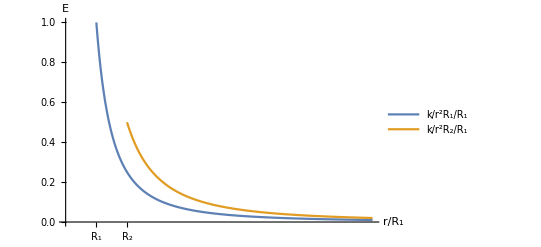

```mathematica
centerPlot@Show[Plot[{1/r^2,-1},{r,1,10},PlotRange->{{0,10},{0,1}},AxesOrigin->{0,0},AxesLabel->{"r/R_1","E"},PlotLegends->{"k/r^2R_1/R_1","k/r^2R_2/R_1"},Ticks->{{{1,"R_1"},{2,"R_2"}},None}],Plot[{2/r^2},{r,2,10},PlotStyle->ColorData[97][2],PlotRange->{{0,10},{0,1}},AxesOrigin->{0,0}]]
```

So only a very tiny bit of charge goes onto the wire, and all the remaining charge will stay on the two spheres. The only remaining point is to discuss our initial assumptions: that only a tiny bit of charge goes onto the wire and that this charge is uniformly distributed along the wire. The first point is discussed in Problem 3.10 where it is shown that a thin wire has essentially zero capacitance. The second point is discussed in Problem 3.5, which is definitely worth a read! □

#### Advanced Section: Electrostatic Pressure

One curious result that emerges from the properties of a conductor is an electrostatic outwards pressure from all charged surfaces on a conductor. To be quantitative about this, recall that the electric field inside the conductor is E_inside=0, while the electric field right outside the conductor is given by (E⃗)_outside=σ/ϵ_0 n̂, where σ is the surface charge density at that patch and n̂ points outwards from the surface. We know that the electric field must point away from the surface, and the magnitude σ/ϵ_0 follows from the fact that an infinite sheet with constant charge density σ generates discontinuity of σ/ϵ_0 across it, and any patch on a conductor looks like an infinite sheet if you get close enough. The electric field exactly on the surface of the conductor is given by the average of these two quantities, namely (E⃗)_surface=((E⃗)_inside+(E⃗)_outside)/2=σ/(2 ϵ_0)n̂.

So what is the pressure (force per unit area) that the patch with charge density σ at the surface of a conductor feels? The pressure P can be written as

(force per unit area)=(force per unit charge)(charge per unit area)

or equivalent

P=E σ=σ^2/(2 ϵ_0)

Note that this points outwards regardless of whether σ is positive or negative. This implies that every small patch with non-zero charge on the surface of a conductor feels a pressure outwards.

#### Recommended Problems

This is a list of excellent problems (with solutions) in David Morin’s book.

3.4 Charge distribution on a conducting disk - Guaranteed to blow your mind!

3.5 Charge distribution on a conducting stick

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered